```mathematica
Rh=A/P;
V=1/n*Rh^(2/3)*Sqrt[s];
Q==A*V
```

Q==(A (A/P)^(2/3) √s)/n

### Dane: Q, kształt kanału, s i n; szukane: Y

#### Kanał prostokątny

```mathematica
Fprostokatny=(A*V-Q)/.{A->B*Y, P->2Y+B}
FullSimplify[Fprostokatny*n]
FullSimplify[Fprostokatny*n/(B*Sqrt[s])]
FullSimplify[Fprostokatny*n/(B*Sqrt[s])/B^(2/3)] (*wzór ze skryptu*)
FullSimplify[D[Fprostokatny*n/(B*Sqrt[s])/B^(2/3),Y]](*pochodna ze skryptu*)
```

-Q+(B √s Y ((B Y)/(B+2 Y))^(2/3))/n

-n Q+B √s Y ((B Y)/(B+2 Y))^(2/3)

-(n Q)/(B √s)+Y ((B Y)/(B+2 Y))^(2/3)

(-(n Q)/(√s)+B Y ((B Y)/(B+2 Y))^(2/3))/B^(5/3)

(((B Y)/(B+2 Y))^(5/3) (5 B+6 Y))/(3 B^(5/3) Y)

```mathematica
Assuming[B>0,FullSimplify[Fprostokatny*n/(B*Sqrt[s])/B^(2/3)-((Y^(5/3))/((2Y+B)^(2/3))-n*Q/(B^(5/3)*Sqrt[s]))]] (*test wzoru ze skryptu*)
Assuming[B>0,FullSimplify[D[Fprostokatny*n/(B*Sqrt[s])/B^(2/3),Y]-((5/3*Y^(2/3)*(B+2Y)^(2/3)-4/3*Y^(5/3)*(B+2Y)^(-1/3))/(2Y+B)^(4/3))]] (*test pochodnej ze skryptu*)
```

0

0

#### Kanał trójkątny

```mathematica
Ftrojkatny=(A*V-Q)/.{A->B*(Cot[γ]*B/2)/2,P->2Sqrt[Y^2+(B/2)^2]}/.B->Tan[γ]*Y*2
Solve[Ftrojkatny==0,Y]
```

-Q+(√s Y^2 Tan[γ] ((Y^2 Tan[γ])/(√(Y^2+Y^2 Tan[γ]^2)))^(2/3))/(2^(2/3) n)

{{Y→-((-2)^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→((-2)^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→-(2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→-(ⅈ 2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→(ⅈ 2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→(2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→-((-1)^(3/4) 2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)},{Y→((-1)^(3/4) 2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)}}

```mathematica
FullSimplify[(2^(1/4) (n^3 Q^3 √s Cot[γ]^3+n^3 Q^3 √s Cot[γ]^5)^(1/8))/s^(1/4)-((n*Q)^(3/8)/Tan[γ]^(5/8)*(2*Sqrt[Tan[γ]^2+1])^(1/4)/s^(3/16))]/.{n->0.1,Q->1,s->0.1,γ->Pi/8} (*test wzoru ze skryptu*)
```

-2.34784×10^-16

#### Kanał cylindryczny

```mathematica
Fcylindryczny=(A*V-Q)/.{A-> R^2/2*(θ-Sin[θ]),P->θ*R}
FullSimplify[Fcylindryczny*n*2^(5/3)/Sqrt[s]/R^(8/3)] (*wzór ze skryptu*)
```

-Q+(R^2 √s (θ-Sin[θ]) ((R (θ-Sin[θ]))/θ)^(2/3))/(2 2^(2/3) n)

(-(2 2^(2/3) n Q)/(√s)+R^2 (θ-Sin[θ]) (R-(R Sin[θ])/θ)^(2/3))/R^(8/3)

((-θ+Sin[θ]) ((θ-Sin[θ])^(2/3)-θ^(2/3) (1-Sin[θ]/θ)^(2/3)))/θ^(2/3)

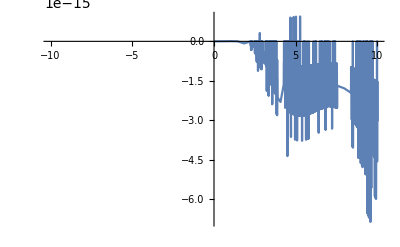

```mathematica
Assuming[R>0,FullSimplify[Fcylindryczny*n*2^(5/3)/Sqrt[s]/R^(8/3)-((θ-Sin[θ])^(5/3)/θ^(2/3)-2^(5/3)*n*Q/R^(8/3)/Sqrt[s])]]
Plot[Assuming[R>0,FullSimplify[Fcylindryczny*n*2^(5/3)/Sqrt[s]/R^(8/3)-((θ-Sin[θ])^(5/3)/θ^(2/3)-2^(5/3)*n*Q/R^(8/3)/Sqrt[s])]],{θ,-10,10}] (*test wzoru ze skryptu*)
```

#### Kanał trapezowy (na ten moment mi się już nie chce)